NDSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[TrueSuperscriptBox[.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.408572 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

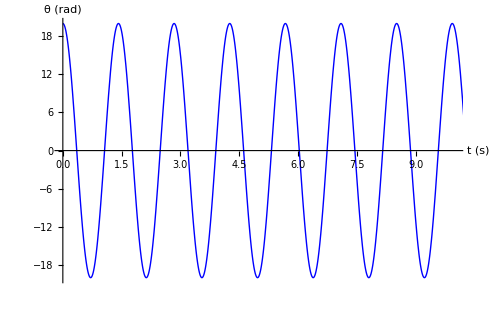

```mathematica
g = 9.8;
l = 0.5;
omega = √(g/l);
θ0 = 20*π/180;
ω0 = 0;

ode1 = {θ''[t] == -(g/l) * Sin[θ[t]], θ[0] == θ0, θ'[0] == ω0};
sol = NDSolve[ode1,θ,{t,0,20}];

approx = (180/Pi) θ0 Cos[omega*t];

myplot = Plot[{approx, (180/Pi) θ[t] /. sol}, {t,0,20},
PlotStyle -> {{Blue},{Dashed, Red}},
AxesLabel -> {"t (s)", "θ (rad)"},
PlotRange -> {{0,10}, {-20, 20}}, ImageSize -> {500, 300}];
Show[myplot]
```